Construction and study of the ground state in the generalized Ising model

Grabovskiy Andrey

Espigule-Pons Bernat

Budker Institute and Novosibirsk State University

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: The goal of the project is to understand what kind of ground states are realized for a generalized Ising model with a given set of energy weights.

SUMMARY OF WORK: 1. Starting from random distributions states with local minimal energy were obtained via Monte Carlo and Cellular automaton techniques.  2. Exhaustive search for small field sizes was done.

RESULTS AND FUTURE  WORK: Fields with even number of states have regular symmetric ground states, fields with odd number of spins may have irregular ground states with high degeneracy.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

The 2 D Ising model is a system of interacting spins placed in the integer points of a rectangular grid. The energy of the system s is given by the list convolution of the weight pattern and the list of spin values s
e[s_, patternNum_] := Apply[Plus, s ListConvolve[pattern, s, 2], {0, 1}]
The weight pattern is defined as 1/2(w4 | w1 | w3
w2 | 0 | w2
w3 | w1 | w4) and the values for w’s ∈ {-2,-1,0,1,2}.
For the a 5x5 matrix s = d_ij for example this convolution reads
e =w1 (d_11 d_21+d_31 d_21+d_12 d_22+d_13 d_23+d_14 d_24+d_22 d_32+d_23 d_33+d_24 d_34+d_11 d_41+d_31 d_41+d_12 d_42+d_32 d_42+d_13 d_43+d_33 d_43+d_14 d_44+d_34 d_44)+w2 (d_11 d_12+d_13 d_12+d_11 d_14+d_13 d_14+d_21 d_22+d_22 d_23+d_21 d_24+d_23 d_24+d_31 d_32+d_32 d_33+d_31 d_34+d_33 d_34+d_41 d_42+d_42 d_43+d_41 d_44+d_43 d_44)+w3 (d_12 d_21+d_34 d_21+d_13 d_22+d_14 d_23+d_11 d_24+d_22 d_31+d_23 d_32+d_24 d_33+d_14 d_41+d_32 d_41+d_11 d_42+d_33 d_42+d_12 d_43+d_34 d_43+d_13 d_44+d_31 d_44)+w4 (d_14 d_21+d_32 d_21+d_11 d_22+d_12 d_23+d_13 d_24+d_24 d_31+d_22 d_33+d_23 d_34+d_12 d_41+d_34 d_41+d_13 d_42+d_31 d_42+d_14 d_43+d_32 d_43+d_11 d_44+d_33 d_44)

Exhaustive search for ground state on 3x3, 4x4. 5x5, 6x6 fields with periodic boundary conditions.

For example for interaction pattern (0 | 1 | 0
2 | 0 | 2
0 | 1 | 0)  up to rotations and black to white exchange there are 

3x3 	7 states with energy per spin = -2    

4x4      1 state  with energy per spin = -6      

5x5      51 states with energy per spin = -3.6 


	

6x6 	1 state with energy per spin = -6

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

1. A manipulate demonstrating evolution of the system from a randomly generated state to a local minimum energy state via Monte Carlo (MC) algorithm is done for one of the weights.
2. Final states of such evolution were built for systems with all possible weights  w’s ∈ {-2,-1,0,1,2}.
3. 2 cellular automata (CA) which do not locally increase energy in evolution were constracted for systems with nearest neighbour (NN) interaction (w3=w4=0). Manipulates showing this evolution were built all such systems. One of them is shown to be globally energy reducing (nonincreasing). 
4-6. Exhaustive search of the ground state for 3x3 (NN), 4x4, and 5x5 (NN) was done.
7. For 6x6 field only few cases were investigated because of the large computation time. Their ground states read (0 | 1 | 0
2 | 0 | 2
0 | 1 | 0)-> ,(0 | 2 | 1
1 | 0 | 1
1 | 2 | 0)-> ,(0 | 1 | 0
2 | 0 | 2
0 | 1 | 0)-> . (to be checked)
8. A tooltip with the 4x4 ground state was built for the pictures of MC obtained local minima.

Code

## 1.Monte Carlo search for minimal energy configuration

```mathematica
ClearAll[n,field,m,w1,w2,w3,w4,Δe1,position,positions,op];

n=2^6;field=RandomInteger[1,{n,n}]/. 0->-1;w1=2;w2=2;w3=0;w4=0;

Δe1=
position↦((field⟦Mod[#1-1,n,1],Mod[#2+1,n,1]⟧+field⟦Mod[#1+1,n,1],Mod[#2-1,n,1]⟧)w4+(field⟦Mod[#1-1,n,1],Mod[#2-1,n,1]⟧+field⟦Mod[#1+1,n,1],Mod[#2+1,n,1]⟧)w3+(field⟦Mod[#1-1,n,1],#2⟧+field⟦Mod[#1+1,n,1],#2⟧)w1+w2 (field⟦#1,Mod[#2-1,n,1]⟧+field⟦#1,Mod[#2+1,n,1]⟧))field⟦#1,#2⟧&[Sequence@@position];
positions[m_]:=With[{position=RandomInteger[{1,n/m},2]},If[Or@@Flatten@Table[If[Δe1[{#1,#2}]>0,field⟦#1,#2⟧*=-1;True,False
]&[Mod[position⟦1⟧+n/m i,n,1],Mod[position⟦2⟧+n/m j,n,1]],{i,0,m-1},{j,0,m-1}],Sow[field]]]
```

```mathematica
ArrayPlot[field/.-1->0,PixelConstrained->2]
Monitor[op=Reap[Do[positions[16],{monitor,1,500}]]⟦2⟧;//AbsoluteTiming,monitor]
Tooltip[ArrayPlot[field/.-1->0,PixelConstrained->2],"{2,2,0,0}"]
Manipulate[ArrayPlot[op⟦1,l⟧/.-1->0,PixelConstrained->2],{l,1,Length[op⟦1⟧],1},SaveDefinitions->True]
```

-Graphics-

{2.93491,Null}

-Graphics-

## 2. Monte Carlo evolution to for generalized Ising model with different weights

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\grabovsk\Google Drive\Works\Mathematica_Problems\Final_Project\Final-Project

```mathematica
ClearAll[m,w1,w2,w3,w4,Δe1,position,positions,Δe2,position,positions1];
field=RandomInteger[1,{n,n}]/. 0->-1;
Δe2[position_,w1_,w2_,w3_,w4_]:=((field⟦Mod[#1-1,n,1],Mod[#2+1,n,1]⟧+field⟦Mod[#1+1,n,1],Mod[#2-1,n,1]⟧)w3+(field⟦Mod[#1-1,n,1],Mod[#2-1,n,1]⟧+field⟦Mod[#1+1,n,1],Mod[#2+1,n,1]⟧)w4+(field⟦Mod[#1-1,n,1],#2⟧+field⟦Mod[#1+1,n,1],#2⟧)w1+w2 (field⟦#1,Mod[#2-1,n,1]⟧+field⟦#1,Mod[#2+1,n,1]⟧))field⟦#1,#2⟧&[Sequence@@position];
positions1[m_,w1_,w2_,w3_,w4_]:=With[{position=RandomInteger[{1,n/m},2]},Do[If[Δe2[{#1,#2},w1,w2,w3,w4]>0,field⟦#1,#2⟧*=-1;]&[Mod[position⟦1⟧+n/m i,n,1],Mod[position⟦2⟧+n/m j,n,1]],{i,0,m-1},{j,0,m-1}]]
```

```mathematica
result0=ParallelTable[(field=RandomInteger[1,{n,n}]/. 0->-1;Do[positions1[16,w1,w2,w3,w4],500];ArrayPlot[field/.-1->0,PixelConstrained->2]->{w1,w2,w3,w4}),{w1,-2,2},{w2,-2,2},{w3,-2,2},{w4,-2,2},{i,1,10}];
```

$Aborted

```mathematica
result0>>"MonteCarlo500-4weights(-2,2)10"
```

```mathematica
result=ParallelTable[(field=RandomInteger[1,{n,n}]/. 0->-1;Do[positions1[16,w1,w2,w3,w4],500];Tooltip[ArrayPlot[field/.-1->0,PixelConstrained->2],{w1,w2,w3,w4}]),{w1,-2,2},{w2,-2,2},{w3,-2,2},{w4,-2,2}]//AbsoluteTiming
```

{955.972,((-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-))}

```mathematica
result>>"MonteCarlo500-4weights(-2,2)"
```

```mathematica
result=<<"MonteCarlo500-4weights(-2,2)";
```

## 3. Cellular Automata reducing energy with random initial conditions

```mathematica
ClearAll[patterns]
stepNumber=20;n=2^6;field=RandomInteger[1,{n,n}]/. 0->-1;ArrayPlot[field/.-1->0,PixelConstrained->2]
```

-Graphics-

```mathematica
patterns={({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),-({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),-({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),({{0, 1, 0}, {-1, 0, -1}, {0, 1, 0}}),({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),-({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}}),-({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}})};
DecreaseEnergy[matrix_,pattern_]:=If[matrix⟦2,2⟧Plus@@Flatten[matrix pattern]>0,-matrix⟦2,2⟧,matrix⟦2,2⟧]
DecreaseEnergy1[matrix_,pattern_]:=If[matrix⟦2,2⟧Plus@@Flatten[matrix pattern]>=0,-matrix⟦2,2⟧,matrix⟦2,2⟧]

tuin=Tuples[{0,1},{3,3}]/. 0->-1;

tuout=Table[Thread[tuin->(DecreaseEnergy[#,patterns⟦i⟧]&/@tuin)]/.-1->0,{i,1,Length[patterns]}];
tuout1=Table[Thread[tuin->(DecreaseEnergy1[#,patterns⟦i⟧]&/@tuin)]/.-1->0,{i,1,Length[patterns]}];

rule[matrix_,a_,ruleNumber_]:=matrix/.tuout⟦ruleNumber⟧
rule1[matrix_,a_,ruleNumber_]:=matrix/.tuout1⟦ruleNumber⟧
```

```mathematica
caFunction0[ruleN_]:=CellularAutomaton[{rule[#1,#2,ruleN]&,{},{1,1}},RandomInteger[1,{n,n}],stepNumber];
caFunction1[ruleN_]:=CellularAutomaton[{rule1[#1,#2,ruleN]&,{},{1,1}},RandomInteger[1,{n,n}],stepNumber];
```

```mathematica
evolution=caFunction0/@Range[Length[patterns]];
evolution1=caFunction1/@Range[Length[patterns]];
```

```mathematica
e[s_,patternNum_]:=Apply[Plus,s ListConvolve[patterns⟦patternNum⟧,s,2],{0,1}]
```

```mathematica
allenergies=Table[e[evolution⟦j,i⟧,j],{j,1,Length[patterns]},{i,1,stepNumber}];
```

```mathematica
Manipulate[Grid[Partition[Row[{ArrayPlot[evolution⟦#,i⟧,PixelConstrained->2,PlotLabel->"E = "<>ToString[allenergies⟦#,i⟧]],Spacer[3],
ListPlot[{allenergies⟦#⟧,{{i,allenergies⟦#,i⟧}}},PlotRange->All,ImageSize->200,PlotStyle->PointSize[Large],AxesLabel->{"Step"}]}]&/@Range[Length[patterns]],3],Frame->All],{i,1,stepNumber,1},SaveDefinitions->True]
```

```mathematica
allenergies1=Table[e[evolution1⟦j,i⟧,j],{j,1,Length[patterns]},{i,1,stepNumber}];
```

```mathematica
Manipulate[Grid[Partition[Row[{ArrayPlot[evolution1⟦#,i⟧,PixelConstrained->2,PlotLabel->"E = "<>ToString[allenergies1⟦#,i⟧]],Spacer[3],
ListPlot[{allenergies1⟦#⟧,{{i,allenergies1⟦#,i⟧}}},PlotRange->All,ImageSize->200,PlotStyle->PointSize[Large]]}]&/@Range[Length[patterns]],3],Frame->All],{i,1,stepNumber,1},SaveDefinitions->True]
```

#### We can find the number of the cellular automaton

```mathematica
Length@tuout⟦1⟧
rulNum=FromDigits[Reverse@tuout⟦1,All,-1⟧,2]
```

512

10433933196726529460308090992770263505941990905396726604193420119586037344481001651934410752163403101529675309988122458192246929623401124412153715962879

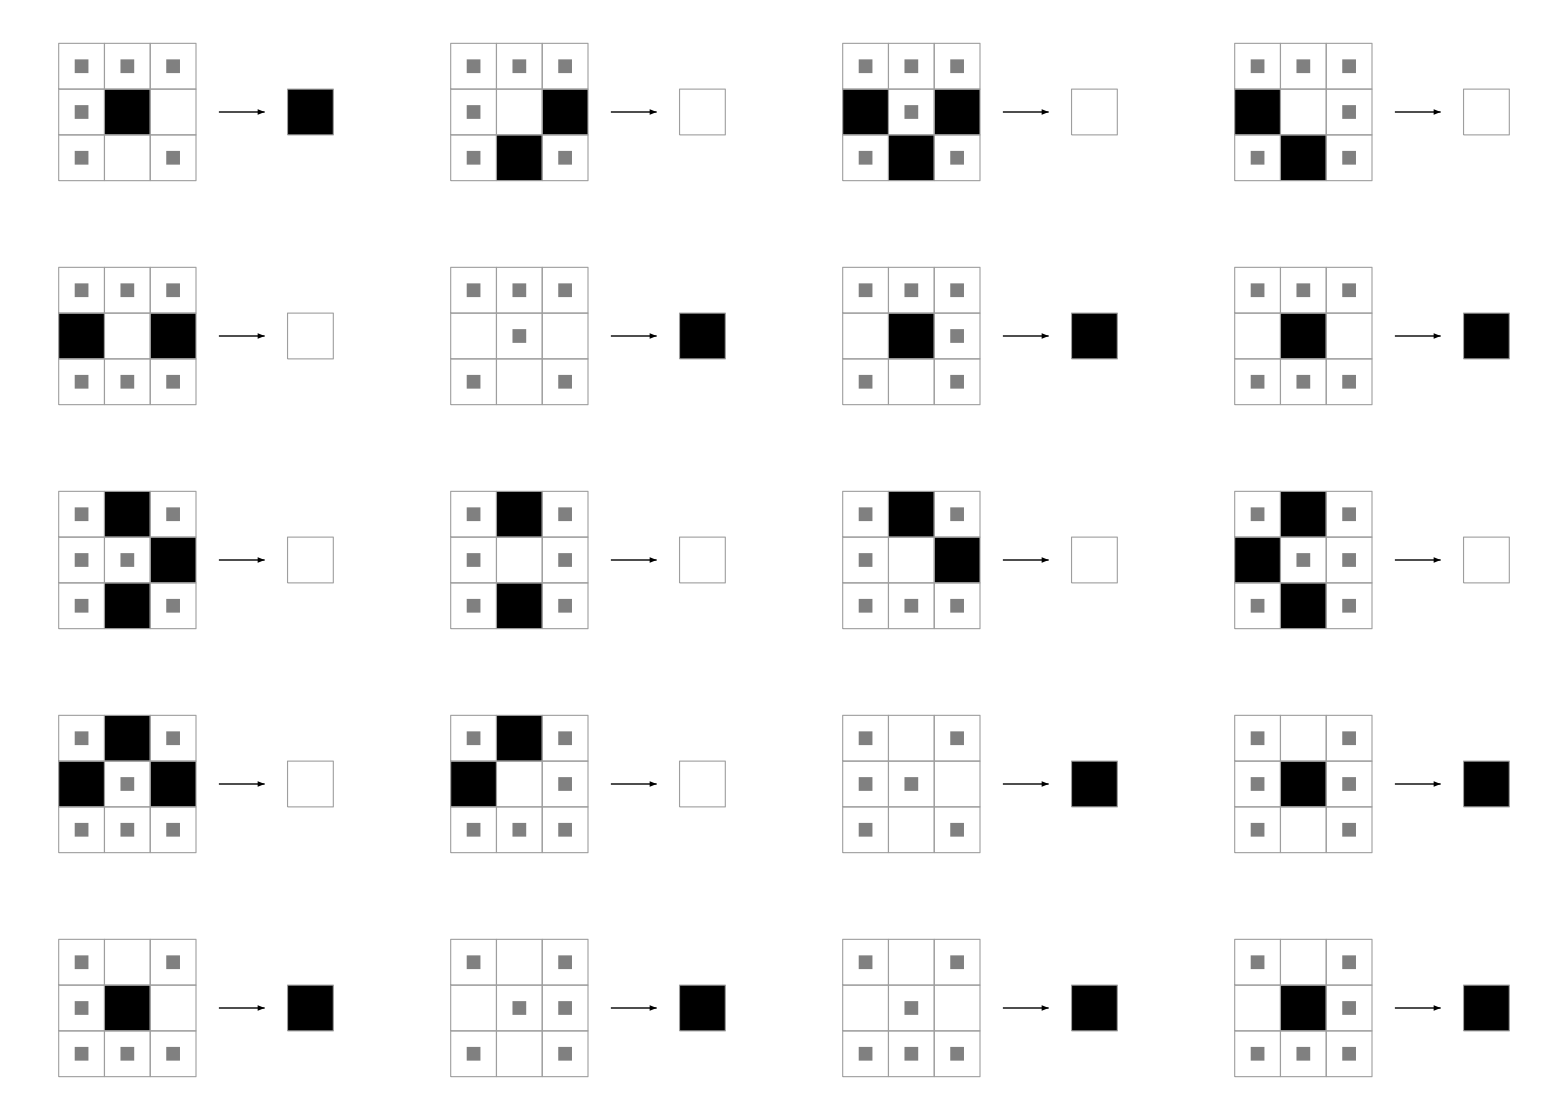

```mathematica
RulePlot[CellularAutomaton[{rulNum,2,{1,1}}],Appearance->"Simplified"]
```

## 4. Exhaustive search 3x3

```mathematica
patterns={({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),-({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),-({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),({{0, 1, 0}, {-1, 0, -1}, {0, 1, 0}}),({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),-({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}}),-({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}})};
```

```mathematica
lattice=Tuples[{0,1},{#,#}]&[3]/. 0->-1;
```

```mathematica
e[s_,patternNum_]:=Apply[Plus,s ListConvolve[patterns⟦patternNum⟧,s,2],{0,1}]
```

```mathematica
factorOutRotations[minE1_,size_] := Block[{minE = minE1, n = 1}, While[n < Length[minE],
      With[{equivalentsets = Table[RotateLeft[RotateLeft[Partition[IntegerDigits[minE[[n]], 2,size^2], size], k]ᵀ, j]ᵀ, {k, 0, size-1}, {j, 0, size-1}]},minE = Cases[minE, Except[Alternatives @@Rest@ Union@Flatten@Map[FromDigits[Flatten[#], 2] &, Join[equivalentsets,equivalentsets/.{0->1,1->0}], {2}]]]]; n++;]; minE]
```

```mathematica
exhausiveEnergies=Table[e[#,j]&/@lattice,{j,1,Length[patterns]}];
minEnergies=Min/@exhausiveEnergies
```

{-12,-36,-18,-54,-24,-42,-30,-6,-18}

```mathematica
energyMinimumPositions=MapThread[Position][{exhausiveEnergies,minEnergies}];
```

```mathematica
res4=Map[FromDigits[Flatten[lattice⟦#⟧/.-1->0],2]&,energyMinimumPositions,{3}];
```

```mathematica
groundState=factorOutRotations[#,3]&/@(Flatten[res4,{3}]⟦1⟧)
```

{{78,84,85,86,98,99,102},{0},{78,84,85,86,98,99,102},{0},{7},{7},{73},{7,14,15,28,29,30,31,78,84,85,86,98,99,102},{0,73}}

```mathematica
Row/@Map[ArrayPlot[Partition[IntegerDigits[#,2,9],3],PixelConstrained->10]&,groundState,{2}]
```

{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics--Graphics-}

## 5. Exhaustive search 4x4

```mathematica
patterns={({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),-({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),-({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),({{0, 1, 0}, {-1, 0, -1}, {0, 1, 0}}),({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),-({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}}),-({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}})};
```

```mathematica
lattice4=Tuples[{0,1},{#,#}]&[4]/. 0->-1;
```

```mathematica
e[s_,patternNum_]:=Apply[Plus,s ListConvolve[patterns⟦patternNum⟧,s,2],{0,1}]
```

```mathematica
Monitor[exhausiveEnergies4=Table[e[#,j]&/@lattice4,{j,1,Length[patterns]-2}];,j]
minEnergies4=Min/@exhausiveEnergies4
```

{-64,-64,-96,-96,-64,-96,-96}

```mathematica
energyMinimumPositions4=MapThread[Position][{exhausiveEnergies4,minEnergies4}];
```

```mathematica
groundstates4=Map[ArrayPlot[lattice4⟦#⟧/.-1->0,PixelConstrained->10]&,energyMinimumPositions4,{3}]
```

({-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-})

## 6. Exhaustive search 5x5

```mathematica
energyCompiled5=Compile[{{fieldN,_Integer},{w1,_Integer},{w2,_Integer},{w3,_Integer},{w4,_Integer}},Block[{d=Partition[N[IntegerDigits[fieldN,2,25]]/. 0. ->-1.,5]},w3 (d⟦1,2⟧ d⟦2,1⟧+d⟦3,5⟧ d⟦2,1⟧+d⟦1,3⟧ d⟦2,2⟧+d⟦1,4⟧ d⟦2,3⟧+d⟦1,5⟧ d⟦2,4⟧+d⟦1,1⟧ d⟦2,5⟧+d⟦2,2⟧ d⟦3,1⟧+d⟦2,3⟧ d⟦3,2⟧+d⟦2,4⟧ d⟦3,3⟧+d⟦2,5⟧ d⟦3,4⟧+d⟦3,2⟧ d⟦4,1⟧+d⟦3,3⟧ d⟦4,2⟧+d⟦3,4⟧ d⟦4,3⟧+d⟦3,5⟧ d⟦4,4⟧+d⟦3,1⟧ d⟦4,5⟧+d⟦1,5⟧ d⟦5,1⟧+d⟦4,2⟧ d⟦5,1⟧+d⟦1,1⟧ d⟦5,2⟧+d⟦4,3⟧ d⟦5,2⟧+d⟦1,2⟧ d⟦5,3⟧+d⟦4,4⟧ d⟦5,3⟧+d⟦1,3⟧ d⟦5,4⟧+d⟦4,5⟧ d⟦5,4⟧+d⟦1,4⟧ d⟦5,5⟧+d⟦4,1⟧ d⟦5,5⟧)+w4 (d⟦1,5⟧ d⟦2,1⟧+d⟦3,2⟧ d⟦2,1⟧+d⟦1,1⟧ d⟦2,2⟧+d⟦1,2⟧ d⟦2,3⟧+d⟦1,3⟧ d⟦2,4⟧+d⟦1,4⟧ d⟦2,5⟧+d⟦2,5⟧ d⟦3,1⟧+d⟦2,2⟧ d⟦3,3⟧+d⟦2,3⟧ d⟦3,4⟧+d⟦2,4⟧ d⟦3,5⟧+d⟦3,5⟧ d⟦4,1⟧+d⟦3,1⟧ d⟦4,2⟧+d⟦3,2⟧ d⟦4,3⟧+d⟦3,3⟧ d⟦4,4⟧+d⟦3,4⟧ d⟦4,5⟧+d⟦1,2⟧ d⟦5,1⟧+d⟦4,5⟧ d⟦5,1⟧+d⟦1,3⟧ d⟦5,2⟧+d⟦4,1⟧ d⟦5,2⟧+d⟦1,4⟧ d⟦5,3⟧+d⟦4,2⟧ d⟦5,3⟧+d⟦1,5⟧ d⟦5,4⟧+d⟦4,3⟧ d⟦5,4⟧+d⟦1,1⟧ d⟦5,5⟧+d⟦4,4⟧ d⟦5,5⟧)+w1 (d⟦1,1⟧ d⟦2,1⟧+d⟦3,1⟧ d⟦2,1⟧+d⟦1,2⟧ d⟦2,2⟧+d⟦1,3⟧ d⟦2,3⟧+d⟦1,4⟧ d⟦2,4⟧+d⟦1,5⟧ d⟦2,5⟧+d⟦2,2⟧ d⟦3,2⟧+d⟦2,3⟧ d⟦3,3⟧+d⟦2,4⟧ d⟦3,4⟧+d⟦2,5⟧ d⟦3,5⟧+d⟦3,1⟧ d⟦4,1⟧+d⟦3,2⟧ d⟦4,2⟧+d⟦3,3⟧ d⟦4,3⟧+d⟦3,4⟧ d⟦4,4⟧+d⟦3,5⟧ d⟦4,5⟧+d⟦1,1⟧ d⟦5,1⟧+d⟦4,1⟧ d⟦5,1⟧+d⟦1,2⟧ d⟦5,2⟧+d⟦4,2⟧ d⟦5,2⟧+d⟦1,3⟧ d⟦5,3⟧+d⟦4,3⟧ d⟦5,3⟧+d⟦1,4⟧ d⟦5,4⟧+d⟦4,4⟧ d⟦5,4⟧+d⟦1,5⟧ d⟦5,5⟧+d⟦4,5⟧ d⟦5,5⟧)+w2 (d⟦1,1⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,4⟧+d⟦1,1⟧ d⟦1,5⟧+d⟦1,4⟧ d⟦1,5⟧+d⟦2,1⟧ d⟦2,2⟧+d⟦2,2⟧ d⟦2,3⟧+d⟦2,3⟧ d⟦2,4⟧+d⟦2,1⟧ d⟦2,5⟧+d⟦2,4⟧ d⟦2,5⟧+d⟦3,1⟧ d⟦3,2⟧+d⟦3,2⟧ d⟦3,3⟧+d⟦3,3⟧ d⟦3,4⟧+d⟦3,1⟧ d⟦3,5⟧+d⟦3,4⟧ d⟦3,5⟧+d⟦4,1⟧ d⟦4,2⟧+d⟦4,2⟧ d⟦4,3⟧+d⟦4,3⟧ d⟦4,4⟧+d⟦4,1⟧ d⟦4,5⟧+d⟦4,4⟧ d⟦4,5⟧+d⟦5,1⟧ d⟦5,2⟧+d⟦5,2⟧ d⟦5,3⟧+d⟦5,3⟧ d⟦5,4⟧+d⟦5,1⟧ d⟦5,5⟧+d⟦5,4⟧ d⟦5,5⟧)],CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True},
RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
factorOutRotations[minE1_,size_] := Block[{minE = minE1, n = 1}, While[n < Length[minE],
      With[{equivalentsets = Table[RotateLeft[RotateLeft[Partition[IntegerDigits[minE[[n]], 2,size^2], size], k]ᵀ, j]ᵀ, {k, 0, size-1}, {j, 0, size-1}]},minE = Cases[minE, Except[Alternatives @@Rest@ Union@Flatten@Map[FromDigits[Flatten[#], 2] &, Join[equivalentsets,equivalentsets/.{0->1,1->0}], {2}]]]]; n++;]; minE]
```

```mathematica
res=Table[If[w2 w1≠0,{w1,w2,0,0}->factorOutRotations[Flatten[Position[#,Min[#]]-1],5]&[ParallelMap[energyCompiled5[#,w1,w2,0,0]&,Range[0,2^25-1],{1}]]],{w1,-2,2},{w2,-2,2}]
```

({-2,-2,0,0}→{0} | {-2,-1,0,0}→{0} | Null | {-2,1,0,0}→{5412005} | {-2,2,0,0}→{5412005}
{-1,-2,0,0}→{0} | {-1,-1,0,0}→{0} | Null | {-1,1,0,0}→{5412005} | {-1,2,0,0}→{5412005}
Null | Null | Null | Null | Null
{1,-2,0,0}→{31775} | {1,-1,0,0}→{31775} | Null | {1,1,0,0}→{5433530,5556410,5556658,5556666,5560506,5560626,5560630,5560634,5560754,5560762,5564602,5591346,5591350,5591354,5591414,5591482,5592250,5592374,5592378,5592405,5592406,5592410,5593274,5593398,5593402,5597370,5842106,5842570,5842571,5842586,5842618,5842633,5842635,5842650,5843130,5843642,5844154,5844619,5844634,5846202,5846603,5846605,5846618,5846667,5846682,5846714,5859514,5909690,5910155,5910170,5925050} | {1,2,0,0}→{5433530,5556410,5556658,5556666,5560506,5560626,5560630,5560634,5560754,5560762,5564602,5591346,5591350,5591354,5591414,5591482,5592250,5592374,5592378,5592405,5592406,5592410,5593274,5593398,5593402,5597370,5842106,5842570,5842571,5842586,5842618,5842633,5842635,5842650,5843130,5843642,5844154,5844619,5844634,5846202,5846603,5846605,5846618,5846667,5846682,5846714,5859514,5909690,5910155,5910170,5925050}
{2,-2,0,0}→{31775} | {2,-1,0,0}→{31775} | Null | {2,1,0,0}→{5433530,5556410,5556658,5556666,5560506,5560626,5560630,5560634,5560754,5560762,5564602,5591346,5591350,5591354,5591414,5591482,5592250,5592374,5592378,5592405,5592406,5592410,5593274,5593398,5593402,5597370,5842106,5842570,5842571,5842586,5842618,5842633,5842635,5842650,5843130,5843642,5844154,5844619,5844634,5846202,5846603,5846605,5846618,5846667,5846682,5846714,5859514,5909690,5910155,5910170,5925050} | {2,2,0,0}→{5433530,5556410,5556658,5556666,5560506,5560626,5560630,5560634,5560754,5560762,5564602,5591346,5591350,5591354,5591414,5591482,5592250,5592374,5592378,5592405,5592406,5592410,5593274,5593398,5593402,5597370,5842106,5842570,5842571,5842586,5842618,5842633,5842635,5842650,5843130,5843642,5844154,5844619,5844634,5846202,5846603,5846605,5846618,5846667,5846682,5846714,5859514,5909690,5910155,5910170,5925050})

```mathematica
res1=Column@DeleteCases[Flatten@res,Null]/.(a_->b_):>a->Row[ (ArrayPlot[Partition[IntegerDigits[#,2,25],5],PixelConstrained->10]&/@b)]
```

{-2,-2,0,0}→-Graphics-
{-2,-1,0,0}→-Graphics-
{-2,1,0,0}→-Graphics-
{-2,2,0,0}→-Graphics-
{-1,-2,0,0}→-Graphics-
{-1,-1,0,0}→-Graphics-
{-1,1,0,0}→-Graphics-
{-1,2,0,0}→-Graphics-
{1,-2,0,0}→-Graphics-
{1,-1,0,0}→-Graphics-
{1,1,0,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,2,0,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,-2,0,0}→-Graphics-
{2,-1,0,0}→-Graphics-
{2,1,0,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,2,0,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
E5=energyCompiled5[5433530,4,2,0,0]/25
```

-3.6

## 7. Exhaustive search 6x6

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
energyCompiled6=Compile[{{fieldN,_Integer},{w1,_Integer},{w2,_Integer},{w3,_Integer},{w4,_Integer}},
Block[{d=Partition[N[IntegerDigits[fieldN,2,36]]/. 0. ->-1.,6]}, w3 (d⟦1,2⟧ d⟦2,1⟧+d⟦3,6⟧ d⟦2,1⟧+d⟦1,3⟧ d⟦2,2⟧+d⟦1,4⟧ d⟦2,3⟧+d⟦1,5⟧ d⟦2,4⟧+d⟦1,6⟧ d⟦2,5⟧+d⟦1,1⟧ d⟦2,6⟧+d⟦2,2⟧ d⟦3,1⟧+d⟦2,3⟧ d⟦3,2⟧+d⟦2,4⟧ d⟦3,3⟧+d⟦2,5⟧ d⟦3,4⟧+d⟦2,6⟧ d⟦3,5⟧+d⟦3,2⟧ d⟦4,1⟧+d⟦3,3⟧ d⟦4,2⟧+d⟦3,4⟧ d⟦4,3⟧+d⟦3,5⟧ d⟦4,4⟧+d⟦3,6⟧ d⟦4,5⟧+d⟦3,1⟧ d⟦4,6⟧+d⟦4,2⟧ d⟦5,1⟧+d⟦4,3⟧ d⟦5,2⟧+d⟦4,4⟧ d⟦5,3⟧+d⟦4,5⟧ d⟦5,4⟧+d⟦4,6⟧ d⟦5,5⟧+d⟦4,1⟧ d⟦5,6⟧+d⟦1,6⟧ d⟦6,1⟧+d⟦5,2⟧ d⟦6,1⟧+d⟦1,1⟧ d⟦6,2⟧+d⟦5,3⟧ d⟦6,2⟧+d⟦1,2⟧ d⟦6,3⟧+d⟦5,4⟧ d⟦6,3⟧+d⟦1,3⟧ d⟦6,4⟧+d⟦5,5⟧ d⟦6,4⟧+d⟦1,4⟧ d⟦6,5⟧+d⟦5,6⟧ d⟦6,5⟧+d⟦1,5⟧ d⟦6,6⟧+d⟦5,1⟧ d⟦6,6⟧)
+w4 (d⟦1,6⟧ d⟦2,1⟧+d⟦3,2⟧ d⟦2,1⟧+d⟦1,1⟧ d⟦2,2⟧+d⟦1,2⟧ d⟦2,3⟧+d⟦1,3⟧ d⟦2,4⟧+d⟦1,4⟧ d⟦2,5⟧+d⟦1,5⟧ d⟦2,6⟧+d⟦2,6⟧ d⟦3,1⟧+d⟦2,2⟧ d⟦3,3⟧+d⟦2,3⟧ d⟦3,4⟧+d⟦2,4⟧ d⟦3,5⟧+d⟦2,5⟧ d⟦3,6⟧+d⟦3,6⟧ d⟦4,1⟧+d⟦3,1⟧ d⟦4,2⟧+d⟦3,2⟧ d⟦4,3⟧+d⟦3,3⟧ d⟦4,4⟧+d⟦3,4⟧ d⟦4,5⟧+d⟦3,5⟧ d⟦4,6⟧+d⟦4,6⟧ d⟦5,1⟧+d⟦4,1⟧ d⟦5,2⟧+d⟦4,2⟧ d⟦5,3⟧+d⟦4,3⟧ d⟦5,4⟧+d⟦4,4⟧ d⟦5,5⟧+d⟦4,5⟧ d⟦5,6⟧+d⟦1,2⟧ d⟦6,1⟧+d⟦5,6⟧ d⟦6,1⟧+d⟦1,3⟧ d⟦6,2⟧+d⟦5,1⟧ d⟦6,2⟧+d⟦1,4⟧ d⟦6,3⟧+d⟦5,2⟧ d⟦6,3⟧+d⟦1,5⟧ d⟦6,4⟧+d⟦5,3⟧ d⟦6,4⟧+d⟦1,6⟧ d⟦6,5⟧+d⟦5,4⟧ d⟦6,5⟧+d⟦1,1⟧ d⟦6,6⟧+d⟦5,5⟧ d⟦6,6⟧)
+w1 (d⟦1,1⟧ d⟦2,1⟧+d⟦3,1⟧ d⟦2,1⟧+d⟦1,2⟧ d⟦2,2⟧+d⟦1,3⟧ d⟦2,3⟧+d⟦1,4⟧ d⟦2,4⟧+d⟦1,5⟧ d⟦2,5⟧+d⟦1,6⟧ d⟦2,6⟧+d⟦2,2⟧ d⟦3,2⟧+d⟦2,3⟧ d⟦3,3⟧+d⟦2,4⟧ d⟦3,4⟧+d⟦2,5⟧ d⟦3,5⟧+d⟦2,6⟧ d⟦3,6⟧+d⟦3,1⟧ d⟦4,1⟧+d⟦3,2⟧ d⟦4,2⟧+d⟦3,3⟧ d⟦4,3⟧+d⟦3,4⟧ d⟦4,4⟧+d⟦3,5⟧ d⟦4,5⟧+d⟦3,6⟧ d⟦4,6⟧+d⟦4,1⟧ d⟦5,1⟧+d⟦4,2⟧ d⟦5,2⟧+d⟦4,3⟧ d⟦5,3⟧+d⟦4,4⟧ d⟦5,4⟧+d⟦4,5⟧ d⟦5,5⟧+d⟦4,6⟧ d⟦5,6⟧+d⟦1,1⟧ d⟦6,1⟧+d⟦5,1⟧ d⟦6,1⟧+d⟦1,2⟧ d⟦6,2⟧+d⟦5,2⟧ d⟦6,2⟧+d⟦1,3⟧ d⟦6,3⟧+d⟦5,3⟧ d⟦6,3⟧+d⟦1,4⟧ d⟦6,4⟧+d⟦5,4⟧ d⟦6,4⟧+d⟦1,5⟧ d⟦6,5⟧+d⟦5,5⟧ d⟦6,5⟧+d⟦1,6⟧ d⟦6,6⟧+d⟦5,6⟧ d⟦6,6⟧)
+w2 (d⟦1,1⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,4⟧+d⟦1,4⟧ d⟦1,5⟧+d⟦1,1⟧ d⟦1,6⟧+d⟦1,5⟧ d⟦1,6⟧+d⟦2,1⟧ d⟦2,2⟧+d⟦2,2⟧ d⟦2,3⟧+d⟦2,3⟧ d⟦2,4⟧+d⟦2,4⟧ d⟦2,5⟧+d⟦2,1⟧ d⟦2,6⟧+d⟦2,5⟧ d⟦2,6⟧+d⟦3,1⟧ d⟦3,2⟧+d⟦3,2⟧ d⟦3,3⟧+d⟦3,3⟧ d⟦3,4⟧+d⟦3,4⟧ d⟦3,5⟧+d⟦3,1⟧ d⟦3,6⟧+d⟦3,5⟧ d⟦3,6⟧+d⟦4,1⟧ d⟦4,2⟧+d⟦4,2⟧ d⟦4,3⟧+d⟦4,3⟧ d⟦4,4⟧+d⟦4,4⟧ d⟦4,5⟧+d⟦4,1⟧ d⟦4,6⟧+d⟦4,5⟧ d⟦4,6⟧+d⟦5,1⟧ d⟦5,2⟧+d⟦5,2⟧ d⟦5,3⟧+d⟦5,3⟧ d⟦5,4⟧+d⟦5,4⟧ d⟦5,5⟧+d⟦5,1⟧ d⟦5,6⟧+d⟦5,5⟧ d⟦5,6⟧+d⟦6,1⟧ d⟦6,2⟧+d⟦6,2⟧ d⟦6,3⟧+d⟦6,3⟧ d⟦6,4⟧+d⟦6,4⟧ d⟦6,5⟧+d⟦6,1⟧ d⟦6,6⟧+d⟦6,5⟧ d⟦6,6⟧)],
CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True},RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
minenergy={{0},energyCompiled6[0,4,2,4,-2]};
findMinEnergyCompiledFully[step_,w1_,w2_,w3_,w4_]:=Block[{field,currentEnergy,t},
Do[t=AbsoluteTiming[field=ParallelMap[energyCompiled6[#,w1,w2,w3,w4]&,Range[step*(n-1),step*n-1],{1}];currentEnergy=Min[field];
If[currentEnergy<=minenergy⟦2⟧,If[currentEnergy==minenergy⟦2⟧,minenergy⟦1⟧=Join[minenergy⟦1⟧,Flatten[Position[field,currentEnergy]-1+step*(n-1)]];,
minenergy={Flatten[Position[field,currentEnergy]-1+step*(n-1)],currentEnergy};];minenergy>>"minenergy"]];
Print[Row@{"Time taken ",t⟦1⟧/60," min.,   step = ",n,"/",2^36/step",  Emin = ",minenergy⟦2⟧,",  # states =",Length[minenergy⟦1⟧]}],{n,1,2^36/step}]]
```

```mathematica
factorOutRotations[minE1_]:=Block[{minE=minE1,n=1},While[n<Length[minE],
With[{equivalentsets=Table[RotateLeft[RotateLeft[Partition[IntegerDigits[minE⟦n⟧,2,36],6],k]ᵀ,j]ᵀ,{k,0,5},{j,0,5}]},
minE=Cases[minE,Except[Alternatives@@Rest@Union@Flatten@Map[FromDigits[Flatten[#],2]&,equivalentsets,{2}]]]];n++;];minE]
```

```mathematica
findMinEnergyCompiledFully[2^27,4,2,4,-2]
```

```mathematica
minenergy1=factorOutRotations[minenergy⟦1⟧]
Length[minenergy1]
ArrayPlot[Partition[N[IntegerDigits[#,2,36]],6],PixelConstrained->5]&/@Take[minenergy1,UpTo[100]]
```

```mathematica
E6=energyCompiled6[FromDigits[Flatten@({{1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}}),2],4,2,0,0]/36
ArrayPlot[({{1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}}),PixelConstrained->10]
```

-6.

-Graphics-

## 8. Comparison of exact ground state for 4x4 and MonteCarlo for 64x64

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\grabovsk\Google Drive\Works\Mathematica_Problems\Final_Project\Final-Project

```mathematica
energyCompiled4=Compile[{{fieldN,_Integer},{w1,_Integer},{w2,_Integer},{w3,_Integer},{w4,_Integer}},
Block[{d=Partition[N[IntegerDigits[fieldN,2,16]]/. 0. ->-1.,4]}, w1 (d⟦1,1⟧ d⟦2,1⟧+d⟦3,1⟧ d⟦2,1⟧+d⟦1,2⟧ d⟦2,2⟧+d⟦1,3⟧ d⟦2,3⟧+d⟦1,4⟧ d⟦2,4⟧+d⟦2,2⟧ d⟦3,2⟧+d⟦2,3⟧ d⟦3,3⟧+d⟦2,4⟧ d⟦3,4⟧+d⟦1,1⟧ d⟦4,1⟧+d⟦3,1⟧ d⟦4,1⟧+d⟦1,2⟧ d⟦4,2⟧+d⟦3,2⟧ d⟦4,2⟧+d⟦1,3⟧ d⟦4,3⟧+d⟦3,3⟧ d⟦4,3⟧+d⟦1,4⟧ d⟦4,4⟧+d⟦3,4⟧ d⟦4,4⟧)+w2 (d⟦1,1⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,2⟧+d⟦1,1⟧ d⟦1,4⟧+d⟦1,3⟧ d⟦1,4⟧+d⟦2,1⟧ d⟦2,2⟧+d⟦2,2⟧ d⟦2,3⟧+d⟦2,1⟧ d⟦2,4⟧+d⟦2,3⟧ d⟦2,4⟧+d⟦3,1⟧ d⟦3,2⟧+d⟦3,2⟧ d⟦3,3⟧+d⟦3,1⟧ d⟦3,4⟧+d⟦3,3⟧ d⟦3,4⟧+d⟦4,1⟧ d⟦4,2⟧+d⟦4,2⟧ d⟦4,3⟧+d⟦4,1⟧ d⟦4,4⟧+d⟦4,3⟧ d⟦4,4⟧)+w3 (d⟦1,2⟧ d⟦2,1⟧+d⟦3,4⟧ d⟦2,1⟧+d⟦1,3⟧ d⟦2,2⟧+d⟦1,4⟧ d⟦2,3⟧+d⟦1,1⟧ d⟦2,4⟧+d⟦2,2⟧ d⟦3,1⟧+d⟦2,3⟧ d⟦3,2⟧+d⟦2,4⟧ d⟦3,3⟧+d⟦1,4⟧ d⟦4,1⟧+d⟦3,2⟧ d⟦4,1⟧+d⟦1,1⟧ d⟦4,2⟧+d⟦3,3⟧ d⟦4,2⟧+d⟦1,2⟧ d⟦4,3⟧+d⟦3,4⟧ d⟦4,3⟧+d⟦1,3⟧ d⟦4,4⟧+d⟦3,1⟧ d⟦4,4⟧)+w4 (d⟦1,4⟧ d⟦2,1⟧+d⟦3,2⟧ d⟦2,1⟧+d⟦1,1⟧ d⟦2,2⟧+d⟦1,2⟧ d⟦2,3⟧+d⟦1,3⟧ d⟦2,4⟧+d⟦2,4⟧ d⟦3,1⟧+d⟦2,2⟧ d⟦3,3⟧+d⟦2,3⟧ d⟦3,4⟧+d⟦1,2⟧ d⟦4,1⟧+d⟦3,4⟧ d⟦4,1⟧+d⟦1,3⟧ d⟦4,2⟧+d⟦3,1⟧ d⟦4,2⟧+d⟦1,4⟧ d⟦4,3⟧+d⟦3,2⟧ d⟦4,3⟧+d⟦1,1⟧ d⟦4,4⟧+d⟦3,3⟧ d⟦4,4⟧)],
CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True},RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
factorOutRotations[minE1_,size_] := Block[{minE = minE1, n = 1}, While[n < Length[minE],With[{equivalentsets = Table[RotateLeft[RotateLeft[Partition[IntegerDigits[minE[[n]], 2,size^2], size], k]ᵀ, j]ᵀ, {k, 0, size-1}, {j, 0, size-1}]},minE = Cases[minE, Except[Alternatives @@Rest@ Union@Flatten@Map[FromDigits[Flatten[#], 2] &, Join[equivalentsets,equivalentsets/.{0->1,1->0}], {2}]]]]; n++;]; minE]
```

```mathematica
res44=Table[Print[{w1,w2,w3,w4}];If[w1==w2==w3==w4==0,{0,0,0,0}->0,{w1,w2,w3,w4}->factorOutRotations[Flatten[Position[#,Min[#]]-1],4]&[ParallelMap[energyCompiled4[#,w1,w2,w3,w4]&,Range[0,2^16-1],{1}]]],{w1,-2,2},{w2,-2,2},{w3,-2,2},{w4,-2,2}];
```

```mathematica
res45=Flatten[res44/.(a_->b_):>a->Row[(ArrayPlot[Partition[IntegerDigits[#,2,16],4],PixelConstrained->10]&/@b),Spacer[20]]];
```

```mathematica
res455=Column/@Partition[res45,25]
```

{{-2,-2,-2,-2}→-Graphics-
{-2,-2,-2,-1}→-Graphics-
{-2,-2,-2,0}→-Graphics-
{-2,-2,-2,1}→-Graphics-
{-2,-2,-2,2}→-Graphics--Graphics-
{-2,-2,-1,-2}→-Graphics-
{-2,-2,-1,-1}→-Graphics-
{-2,-2,-1,0}→-Graphics-
{-2,-2,-1,1}→-Graphics-
{-2,-2,-1,2}→-Graphics--Graphics-
{-2,-2,0,-2}→-Graphics-
{-2,-2,0,-1}→-Graphics-
{-2,-2,0,0}→-Graphics-
{-2,-2,0,1}→-Graphics-
{-2,-2,0,2}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,-2,1,-2}→-Graphics-
{-2,-2,1,-1}→-Graphics-
{-2,-2,1,0}→-Graphics-
{-2,-2,1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,-2,1,2}→-Graphics--Graphics-
{-2,-2,2,-2}→-Graphics--Graphics-
{-2,-2,2,-1}→-Graphics--Graphics-
{-2,-2,2,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,-2,2,1}→-Graphics--Graphics-
{-2,-2,2,2}→-Graphics--Graphics-,{-2,-1,-2,-2}→-Graphics-
{-2,-1,-2,-1}→-Graphics-
{-2,-1,-2,0}→-Graphics-
{-2,-1,-2,1}→-Graphics-
{-2,-1,-2,2}→-Graphics-
{-2,-1,-1,-2}→-Graphics-
{-2,-1,-1,-1}→-Graphics-
{-2,-1,-1,0}→-Graphics-
{-2,-1,-1,1}→-Graphics-
{-2,-1,-1,2}→-Graphics-
{-2,-1,0,-2}→-Graphics-
{-2,-1,0,-1}→-Graphics-
{-2,-1,0,0}→-Graphics-
{-2,-1,0,1}→-Graphics--Graphics--Graphics--Graphics-
{-2,-1,0,2}→-Graphics-
{-2,-1,1,-2}→-Graphics-
{-2,-1,1,-1}→-Graphics-
{-2,-1,1,0}→-Graphics--Graphics--Graphics--Graphics-
{-2,-1,1,1}→-Graphics-
{-2,-1,1,2}→-Graphics-
{-2,-1,2,-2}→-Graphics-
{-2,-1,2,-1}→-Graphics-
{-2,-1,2,0}→-Graphics-
{-2,-1,2,1}→-Graphics-
{-2,-1,2,2}→-Graphics-,{-2,0,-2,-2}→-Graphics-
{-2,0,-2,-1}→-Graphics-
{-2,0,-2,0}→-Graphics-
{-2,0,-2,1}→-Graphics--Graphics-
{-2,0,-2,2}→-Graphics-
{-2,0,-1,-2}→-Graphics-
{-2,0,-1,-1}→-Graphics-
{-2,0,-1,0}→-Graphics-
{-2,0,-1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,0,-1,2}→-Graphics--Graphics-
{-2,0,0,-2}→-Graphics-
{-2,0,0,-1}→-Graphics-
{-2,0,0,0}→-Graphics--Graphics--Graphics--Graphics-
{-2,0,0,1}→-Graphics-
{-2,0,0,2}→-Graphics-
{-2,0,1,-2}→-Graphics--Graphics-
{-2,0,1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,0,1,0}→-Graphics-
{-2,0,1,1}→-Graphics-
{-2,0,1,2}→-Graphics-
{-2,0,2,-2}→-Graphics-
{-2,0,2,-1}→-Graphics--Graphics-
{-2,0,2,0}→-Graphics-
{-2,0,2,1}→-Graphics-
{-2,0,2,2}→-Graphics-,{-2,1,-2,-2}→-Graphics-
{-2,1,-2,-1}→-Graphics-
{-2,1,-2,0}→-Graphics-
{-2,1,-2,1}→-Graphics-
{-2,1,-2,2}→-Graphics-
{-2,1,-1,-2}→-Graphics-
{-2,1,-1,-1}→-Graphics-
{-2,1,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{-2,1,-1,1}→-Graphics-
{-2,1,-1,2}→-Graphics-
{-2,1,0,-2}→-Graphics-
{-2,1,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{-2,1,0,0}→-Graphics-
{-2,1,0,1}→-Graphics-
{-2,1,0,2}→-Graphics-
{-2,1,1,-2}→-Graphics-
{-2,1,1,-1}→-Graphics-
{-2,1,1,0}→-Graphics-
{-2,1,1,1}→-Graphics-
{-2,1,1,2}→-Graphics-
{-2,1,2,-2}→-Graphics-
{-2,1,2,-1}→-Graphics-
{-2,1,2,0}→-Graphics-
{-2,1,2,1}→-Graphics-
{-2,1,2,2}→-Graphics-,{-2,2,-2,-2}→-Graphics--Graphics-
{-2,2,-2,-1}→-Graphics--Graphics-
{-2,2,-2,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,2,-2,1}→-Graphics--Graphics-
{-2,2,-2,2}→-Graphics--Graphics-
{-2,2,-1,-2}→-Graphics--Graphics-
{-2,2,-1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,2,-1,0}→-Graphics-
{-2,2,-1,1}→-Graphics-
{-2,2,-1,2}→-Graphics-
{-2,2,0,-2}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,2,0,-1}→-Graphics-
{-2,2,0,0}→-Graphics-
{-2,2,0,1}→-Graphics-
{-2,2,0,2}→-Graphics-
{-2,2,1,-2}→-Graphics--Graphics-
{-2,2,1,-1}→-Graphics-
{-2,2,1,0}→-Graphics-
{-2,2,1,1}→-Graphics-
{-2,2,1,2}→-Graphics-
{-2,2,2,-2}→-Graphics--Graphics-
{-2,2,2,-1}→-Graphics-
{-2,2,2,0}→-Graphics-
{-2,2,2,1}→-Graphics-
{-2,2,2,2}→-Graphics-,{-1,-2,-2,-2}→-Graphics-
{-1,-2,-2,-1}→-Graphics-
{-1,-2,-2,0}→-Graphics-
{-1,-2,-2,1}→-Graphics-
{-1,-2,-2,2}→-Graphics-
{-1,-2,-1,-2}→-Graphics-
{-1,-2,-1,-1}→-Graphics-
{-1,-2,-1,0}→-Graphics-
{-1,-2,-1,1}→-Graphics-
{-1,-2,-1,2}→-Graphics-
{-1,-2,0,-2}→-Graphics-
{-1,-2,0,-1}→-Graphics-
{-1,-2,0,0}→-Graphics-
{-1,-2,0,1}→-Graphics--Graphics--Graphics--Graphics-
{-1,-2,0,2}→-Graphics-
{-1,-2,1,-2}→-Graphics-
{-1,-2,1,-1}→-Graphics-
{-1,-2,1,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,-2,1,1}→-Graphics-
{-1,-2,1,2}→-Graphics-
{-1,-2,2,-2}→-Graphics-
{-1,-2,2,-1}→-Graphics-
{-1,-2,2,0}→-Graphics-
{-1,-2,2,1}→-Graphics-
{-1,-2,2,2}→-Graphics-,{-1,-1,-2,-2}→-Graphics-
{-1,-1,-2,-1}→-Graphics-
{-1,-1,-2,0}→-Graphics-
{-1,-1,-2,1}→-Graphics--Graphics-
{-1,-1,-2,2}→-Graphics-
{-1,-1,-1,-2}→-Graphics-
{-1,-1,-1,-1}→-Graphics-
{-1,-1,-1,0}→-Graphics-
{-1,-1,-1,1}→-Graphics--Graphics-
{-1,-1,-1,2}→-Graphics-
{-1,-1,0,-2}→-Graphics-
{-1,-1,0,-1}→-Graphics-
{-1,-1,0,0}→-Graphics-
{-1,-1,0,1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-1,-1,0,2}→-Graphics--Graphics--Graphics--Graphics-
{-1,-1,1,-2}→-Graphics--Graphics-
{-1,-1,1,-1}→-Graphics--Graphics-
{-1,-1,1,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-1,-1,1,1}→-Graphics--Graphics-
{-1,-1,1,2}→-Graphics--Graphics-
{-1,-1,2,-2}→-Graphics-
{-1,-1,2,-1}→-Graphics-
{-1,-1,2,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,-1,2,1}→-Graphics--Graphics-
{-1,-1,2,2}→-Graphics--Graphics-,{-1,0,-2,-2}→-Graphics-
{-1,0,-2,-1}→-Graphics-
{-1,0,-2,0}→-Graphics-
{-1,0,-2,1}→-Graphics-
{-1,0,-2,2}→-Graphics-
{-1,0,-1,-2}→-Graphics-
{-1,0,-1,-1}→-Graphics-
{-1,0,-1,0}→-Graphics-
{-1,0,-1,1}→-Graphics-
{-1,0,-1,2}→-Graphics-
{-1,0,0,-2}→-Graphics-
{-1,0,0,-1}→-Graphics-
{-1,0,0,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,0,0,1}→-Graphics-
{-1,0,0,2}→-Graphics-
{-1,0,1,-2}→-Graphics-
{-1,0,1,-1}→-Graphics-
{-1,0,1,0}→-Graphics-
{-1,0,1,1}→-Graphics-
{-1,0,1,2}→-Graphics-
{-1,0,2,-2}→-Graphics-
{-1,0,2,-1}→-Graphics-
{-1,0,2,0}→-Graphics-
{-1,0,2,1}→-Graphics-
{-1,0,2,2}→-Graphics-,{-1,1,-2,-2}→-Graphics--Graphics-
{-1,1,-2,-1}→-Graphics--Graphics-
{-1,1,-2,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,1,-2,1}→-Graphics-
{-1,1,-2,2}→-Graphics-
{-1,1,-1,-2}→-Graphics--Graphics-
{-1,1,-1,-1}→-Graphics--Graphics-
{-1,1,-1,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-1,1,-1,1}→-Graphics--Graphics-
{-1,1,-1,2}→-Graphics--Graphics-
{-1,1,0,-2}→-Graphics--Graphics--Graphics--Graphics-
{-1,1,0,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-1,1,0,0}→-Graphics-
{-1,1,0,1}→-Graphics-
{-1,1,0,2}→-Graphics-
{-1,1,1,-2}→-Graphics-
{-1,1,1,-1}→-Graphics--Graphics-
{-1,1,1,0}→-Graphics-
{-1,1,1,1}→-Graphics-
{-1,1,1,2}→-Graphics-
{-1,1,2,-2}→-Graphics-
{-1,1,2,-1}→-Graphics--Graphics-
{-1,1,2,0}→-Graphics-
{-1,1,2,1}→-Graphics-
{-1,1,2,2}→-Graphics-,{-1,2,-2,-2}→-Graphics-
{-1,2,-2,-1}→-Graphics-
{-1,2,-2,0}→-Graphics-
{-1,2,-2,1}→-Graphics-
{-1,2,-2,2}→-Graphics-
{-1,2,-1,-2}→-Graphics-
{-1,2,-1,-1}→-Graphics-
{-1,2,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,2,-1,1}→-Graphics-
{-1,2,-1,2}→-Graphics-
{-1,2,0,-2}→-Graphics-
{-1,2,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{-1,2,0,0}→-Graphics-
{-1,2,0,1}→-Graphics-
{-1,2,0,2}→-Graphics-
{-1,2,1,-2}→-Graphics-
{-1,2,1,-1}→-Graphics-
{-1,2,1,0}→-Graphics-
{-1,2,1,1}→-Graphics-
{-1,2,1,2}→-Graphics-
{-1,2,2,-2}→-Graphics-
{-1,2,2,-1}→-Graphics-
{-1,2,2,0}→-Graphics-
{-1,2,2,1}→-Graphics-
{-1,2,2,2}→-Graphics-,{0,-2,-2,-2}→-Graphics-
{0,-2,-2,-1}→-Graphics-
{0,-2,-2,0}→-Graphics-
{0,-2,-2,1}→-Graphics--Graphics-
{0,-2,-2,2}→-Graphics-
{0,-2,-1,-2}→-Graphics-
{0,-2,-1,-1}→-Graphics-
{0,-2,-1,0}→-Graphics-
{0,-2,-1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{0,-2,-1,2}→-Graphics--Graphics-
{0,-2,0,-2}→-Graphics-
{0,-2,0,-1}→-Graphics-
{0,-2,0,0}→-Graphics--Graphics--Graphics--Graphics-
{0,-2,0,1}→-Graphics-
{0,-2,0,2}→-Graphics-
{0,-2,1,-2}→-Graphics--Graphics-
{0,-2,1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{0,-2,1,0}→-Graphics-
{0,-2,1,1}→-Graphics-
{0,-2,1,2}→-Graphics-
{0,-2,2,-2}→-Graphics-
{0,-2,2,-1}→-Graphics--Graphics-
{0,-2,2,0}→-Graphics-
{0,-2,2,1}→-Graphics-
{0,-2,2,2}→-Graphics-,{0,-1,-2,-2}→-Graphics-
{0,-1,-2,-1}→-Graphics-
{0,-1,-2,0}→-Graphics-
{0,-1,-2,1}→-Graphics-
{0,-1,-2,2}→-Graphics-
{0,-1,-1,-2}→-Graphics-
{0,-1,-1,-1}→-Graphics-
{0,-1,-1,0}→-Graphics-
{0,-1,-1,1}→-Graphics-
{0,-1,-1,2}→-Graphics-
{0,-1,0,-2}→-Graphics-
{0,-1,0,-1}→-Graphics-
{0,-1,0,0}→-Graphics--Graphics--Graphics--Graphics-
{0,-1,0,1}→-Graphics-
{0,-1,0,2}→-Graphics-
{0,-1,1,-2}→-Graphics-
{0,-1,1,-1}→-Graphics-
{0,-1,1,0}→-Graphics-
{0,-1,1,1}→-Graphics-
{0,-1,1,2}→-Graphics-
{0,-1,2,-2}→-Graphics-
{0,-1,2,-1}→-Graphics-
{0,-1,2,0}→-Graphics-
{0,-1,2,1}→-Graphics-
{0,-1,2,2}→-Graphics-,{0,0,-2,-2}→-Graphics--Graphics-
{0,0,-2,-1}→-Graphics--Graphics-
{0,0,-2,0}→-Graphics--Graphics--Graphics--Graphics-
{0,0,-2,1}→-Graphics-
{0,0,-2,2}→-Graphics-
{0,0,-1,-2}→-Graphics--Graphics-
{0,0,-1,-1}→-Graphics--Graphics-
{0,0,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{0,0,-1,1}→-Graphics-
{0,0,-1,2}→-Graphics-
{0,0,0,-2}→-Graphics--Graphics--Graphics--Graphics-
{0,0,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{0,0,0,0}→Row[0,]
{0,0,0,1}→-Graphics--Graphics--Graphics--Graphics-
{0,0,0,2}→-Graphics--Graphics--Graphics--Graphics-
{0,0,1,-2}→-Graphics-
{0,0,1,-1}→-Graphics-
{0,0,1,0}→-Graphics--Graphics--Graphics--Graphics-
{0,0,1,1}→-Graphics--Graphics-
{0,0,1,2}→-Graphics--Graphics-
{0,0,2,-2}→-Graphics-
{0,0,2,-1}→-Graphics-
{0,0,2,0}→-Graphics--Graphics--Graphics--Graphics-
{0,0,2,1}→-Graphics--Graphics-
{0,0,2,2}→-Graphics--Graphics-,{0,1,-2,-2}→-Graphics-
{0,1,-2,-1}→-Graphics-
{0,1,-2,0}→-Graphics-
{0,1,-2,1}→-Graphics-
{0,1,-2,2}→-Graphics-
{0,1,-1,-2}→-Graphics-
{0,1,-1,-1}→-Graphics-
{0,1,-1,0}→-Graphics-
{0,1,-1,1}→-Graphics-
{0,1,-1,2}→-Graphics-
{0,1,0,-2}→-Graphics-
{0,1,0,-1}→-Graphics-
{0,1,0,0}→-Graphics--Graphics--Graphics--Graphics-
{0,1,0,1}→-Graphics-
{0,1,0,2}→-Graphics-
{0,1,1,-2}→-Graphics-
{0,1,1,-1}→-Graphics-
{0,1,1,0}→-Graphics-
{0,1,1,1}→-Graphics-
{0,1,1,2}→-Graphics-
{0,1,2,-2}→-Graphics-
{0,1,2,-1}→-Graphics-
{0,1,2,0}→-Graphics-
{0,1,2,1}→-Graphics-
{0,1,2,2}→-Graphics-,{0,2,-2,-2}→-Graphics-
{0,2,-2,-1}→-Graphics-
{0,2,-2,0}→-Graphics-
{0,2,-2,1}→-Graphics--Graphics-
{0,2,-2,2}→-Graphics-
{0,2,-1,-2}→-Graphics-
{0,2,-1,-1}→-Graphics-
{0,2,-1,0}→-Graphics-
{0,2,-1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{0,2,-1,2}→-Graphics--Graphics-
{0,2,0,-2}→-Graphics-
{0,2,0,-1}→-Graphics-
{0,2,0,0}→-Graphics--Graphics--Graphics--Graphics-
{0,2,0,1}→-Graphics-
{0,2,0,2}→-Graphics-
{0,2,1,-2}→-Graphics--Graphics-
{0,2,1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{0,2,1,0}→-Graphics-
{0,2,1,1}→-Graphics-
{0,2,1,2}→-Graphics-
{0,2,2,-2}→-Graphics-
{0,2,2,-1}→-Graphics--Graphics-
{0,2,2,0}→-Graphics-
{0,2,2,1}→-Graphics-
{0,2,2,2}→-Graphics-,{1,-2,-2,-2}→-Graphics-
{1,-2,-2,-1}→-Graphics-
{1,-2,-2,0}→-Graphics-
{1,-2,-2,1}→-Graphics-
{1,-2,-2,2}→-Graphics-
{1,-2,-1,-2}→-Graphics-
{1,-2,-1,-1}→-Graphics-
{1,-2,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{1,-2,-1,1}→-Graphics-
{1,-2,-1,2}→-Graphics-
{1,-2,0,-2}→-Graphics-
{1,-2,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{1,-2,0,0}→-Graphics-
{1,-2,0,1}→-Graphics-
{1,-2,0,2}→-Graphics-
{1,-2,1,-2}→-Graphics-
{1,-2,1,-1}→-Graphics-
{1,-2,1,0}→-Graphics-
{1,-2,1,1}→-Graphics-
{1,-2,1,2}→-Graphics-
{1,-2,2,-2}→-Graphics-
{1,-2,2,-1}→-Graphics-
{1,-2,2,0}→-Graphics-
{1,-2,2,1}→-Graphics-
{1,-2,2,2}→-Graphics-,{1,-1,-2,-2}→-Graphics--Graphics-
{1,-1,-2,-1}→-Graphics--Graphics-
{1,-1,-2,0}→-Graphics--Graphics--Graphics--Graphics-
{1,-1,-2,1}→-Graphics-
{1,-1,-2,2}→-Graphics-
{1,-1,-1,-2}→-Graphics--Graphics-
{1,-1,-1,-1}→-Graphics--Graphics-
{1,-1,-1,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,-1,-1,1}→-Graphics--Graphics-
{1,-1,-1,2}→-Graphics--Graphics-
{1,-1,0,-2}→-Graphics--Graphics--Graphics--Graphics-
{1,-1,0,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,-1,0,0}→-Graphics-
{1,-1,0,1}→-Graphics-
{1,-1,0,2}→-Graphics-
{1,-1,1,-2}→-Graphics-
{1,-1,1,-1}→-Graphics--Graphics-
{1,-1,1,0}→-Graphics-
{1,-1,1,1}→-Graphics-
{1,-1,1,2}→-Graphics-
{1,-1,2,-2}→-Graphics-
{1,-1,2,-1}→-Graphics--Graphics-
{1,-1,2,0}→-Graphics-
{1,-1,2,1}→-Graphics-
{1,-1,2,2}→-Graphics-,{1,0,-2,-2}→-Graphics-
{1,0,-2,-1}→-Graphics-
{1,0,-2,0}→-Graphics-
{1,0,-2,1}→-Graphics-
{1,0,-2,2}→-Graphics-
{1,0,-1,-2}→-Graphics-
{1,0,-1,-1}→-Graphics-
{1,0,-1,0}→-Graphics-
{1,0,-1,1}→-Graphics-
{1,0,-1,2}→-Graphics-
{1,0,0,-2}→-Graphics-
{1,0,0,-1}→-Graphics-
{1,0,0,0}→-Graphics--Graphics--Graphics--Graphics-
{1,0,0,1}→-Graphics-
{1,0,0,2}→-Graphics-
{1,0,1,-2}→-Graphics-
{1,0,1,-1}→-Graphics-
{1,0,1,0}→-Graphics-
{1,0,1,1}→-Graphics-
{1,0,1,2}→-Graphics-
{1,0,2,-2}→-Graphics-
{1,0,2,-1}→-Graphics-
{1,0,2,0}→-Graphics-
{1,0,2,1}→-Graphics-
{1,0,2,2}→-Graphics-,{1,1,-2,-2}→-Graphics-
{1,1,-2,-1}→-Graphics-
{1,1,-2,0}→-Graphics-
{1,1,-2,1}→-Graphics--Graphics-
{1,1,-2,2}→-Graphics-
{1,1,-1,-2}→-Graphics-
{1,1,-1,-1}→-Graphics-
{1,1,-1,0}→-Graphics-
{1,1,-1,1}→-Graphics--Graphics-
{1,1,-1,2}→-Graphics-
{1,1,0,-2}→-Graphics-
{1,1,0,-1}→-Graphics-
{1,1,0,0}→-Graphics-
{1,1,0,1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,1,0,2}→-Graphics--Graphics--Graphics--Graphics-
{1,1,1,-2}→-Graphics--Graphics-
{1,1,1,-1}→-Graphics--Graphics-
{1,1,1,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,1,1,1}→-Graphics--Graphics-
{1,1,1,2}→-Graphics--Graphics-
{1,1,2,-2}→-Graphics-
{1,1,2,-1}→-Graphics-
{1,1,2,0}→-Graphics--Graphics--Graphics--Graphics-
{1,1,2,1}→-Graphics--Graphics-
{1,1,2,2}→-Graphics--Graphics-,{1,2,-2,-2}→-Graphics-
{1,2,-2,-1}→-Graphics-
{1,2,-2,0}→-Graphics-
{1,2,-2,1}→-Graphics-
{1,2,-2,2}→-Graphics-
{1,2,-1,-2}→-Graphics-
{1,2,-1,-1}→-Graphics-
{1,2,-1,0}→-Graphics-
{1,2,-1,1}→-Graphics-
{1,2,-1,2}→-Graphics-
{1,2,0,-2}→-Graphics-
{1,2,0,-1}→-Graphics-
{1,2,0,0}→-Graphics-
{1,2,0,1}→-Graphics--Graphics--Graphics--Graphics-
{1,2,0,2}→-Graphics-
{1,2,1,-2}→-Graphics-
{1,2,1,-1}→-Graphics-
{1,2,1,0}→-Graphics--Graphics--Graphics--Graphics-
{1,2,1,1}→-Graphics-
{1,2,1,2}→-Graphics-
{1,2,2,-2}→-Graphics-
{1,2,2,-1}→-Graphics-
{1,2,2,0}→-Graphics-
{1,2,2,1}→-Graphics-
{1,2,2,2}→-Graphics-,{2,-2,-2,-2}→-Graphics--Graphics-
{2,-2,-2,-1}→-Graphics--Graphics-
{2,-2,-2,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,-2,-2,1}→-Graphics--Graphics-
{2,-2,-2,2}→-Graphics--Graphics-
{2,-2,-1,-2}→-Graphics--Graphics-
{2,-2,-1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,-2,-1,0}→-Graphics-
{2,-2,-1,1}→-Graphics-
{2,-2,-1,2}→-Graphics-
{2,-2,0,-2}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,-2,0,-1}→-Graphics-
{2,-2,0,0}→-Graphics-
{2,-2,0,1}→-Graphics-
{2,-2,0,2}→-Graphics-
{2,-2,1,-2}→-Graphics--Graphics-
{2,-2,1,-1}→-Graphics-
{2,-2,1,0}→-Graphics-
{2,-2,1,1}→-Graphics-
{2,-2,1,2}→-Graphics-
{2,-2,2,-2}→-Graphics--Graphics-
{2,-2,2,-1}→-Graphics-
{2,-2,2,0}→-Graphics-
{2,-2,2,1}→-Graphics-
{2,-2,2,2}→-Graphics-,{2,-1,-2,-2}→-Graphics-
{2,-1,-2,-1}→-Graphics-
{2,-1,-2,0}→-Graphics-
{2,-1,-2,1}→-Graphics-
{2,-1,-2,2}→-Graphics-
{2,-1,-1,-2}→-Graphics-
{2,-1,-1,-1}→-Graphics-
{2,-1,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{2,-1,-1,1}→-Graphics-
{2,-1,-1,2}→-Graphics-
{2,-1,0,-2}→-Graphics-
{2,-1,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{2,-1,0,0}→-Graphics-
{2,-1,0,1}→-Graphics-
{2,-1,0,2}→-Graphics-
{2,-1,1,-2}→-Graphics-
{2,-1,1,-1}→-Graphics-
{2,-1,1,0}→-Graphics-
{2,-1,1,1}→-Graphics-
{2,-1,1,2}→-Graphics-
{2,-1,2,-2}→-Graphics-
{2,-1,2,-1}→-Graphics-
{2,-1,2,0}→-Graphics-
{2,-1,2,1}→-Graphics-
{2,-1,2,2}→-Graphics-,{2,0,-2,-2}→-Graphics-
{2,0,-2,-1}→-Graphics-
{2,0,-2,0}→-Graphics-
{2,0,-2,1}→-Graphics--Graphics-
{2,0,-2,2}→-Graphics-
{2,0,-1,-2}→-Graphics-
{2,0,-1,-1}→-Graphics-
{2,0,-1,0}→-Graphics-
{2,0,-1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{2,0,-1,2}→-Graphics--Graphics-
{2,0,0,-2}→-Graphics-
{2,0,0,-1}→-Graphics-
{2,0,0,0}→-Graphics--Graphics--Graphics--Graphics-
{2,0,0,1}→-Graphics-
{2,0,0,2}→-Graphics-
{2,0,1,-2}→-Graphics--Graphics-
{2,0,1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{2,0,1,0}→-Graphics-
{2,0,1,1}→-Graphics-
{2,0,1,2}→-Graphics-
{2,0,2,-2}→-Graphics-
{2,0,2,-1}→-Graphics--Graphics-
{2,0,2,0}→-Graphics-
{2,0,2,1}→-Graphics-
{2,0,2,2}→-Graphics-,{2,1,-2,-2}→-Graphics-
{2,1,-2,-1}→-Graphics-
{2,1,-2,0}→-Graphics-
{2,1,-2,1}→-Graphics-
{2,1,-2,2}→-Graphics-
{2,1,-1,-2}→-Graphics-
{2,1,-1,-1}→-Graphics-
{2,1,-1,0}→-Graphics-
{2,1,-1,1}→-Graphics-
{2,1,-1,2}→-Graphics-
{2,1,0,-2}→-Graphics-
{2,1,0,-1}→-Graphics-
{2,1,0,0}→-Graphics-
{2,1,0,1}→-Graphics--Graphics--Graphics--Graphics-
{2,1,0,2}→-Graphics-
{2,1,1,-2}→-Graphics-
{2,1,1,-1}→-Graphics-
{2,1,1,0}→-Graphics--Graphics--Graphics--Graphics-
{2,1,1,1}→-Graphics-
{2,1,1,2}→-Graphics-
{2,1,2,-2}→-Graphics-
{2,1,2,-1}→-Graphics-
{2,1,2,0}→-Graphics-
{2,1,2,1}→-Graphics-
{2,1,2,2}→-Graphics-,{2,2,-2,-2}→-Graphics-
{2,2,-2,-1}→-Graphics-
{2,2,-2,0}→-Graphics-
{2,2,-2,1}→-Graphics-
{2,2,-2,2}→-Graphics--Graphics-
{2,2,-1,-2}→-Graphics-
{2,2,-1,-1}→-Graphics-
{2,2,-1,0}→-Graphics-
{2,2,-1,1}→-Graphics-
{2,2,-1,2}→-Graphics--Graphics-
{2,2,0,-2}→-Graphics-
{2,2,0,-1}→-Graphics-
{2,2,0,0}→-Graphics-
{2,2,0,1}→-Graphics-
{2,2,0,2}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,2,1,-2}→-Graphics-
{2,2,1,-1}→-Graphics-
{2,2,1,0}→-Graphics-
{2,2,1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,2,1,2}→-Graphics--Graphics-
{2,2,2,-2}→-Graphics--Graphics-
{2,2,2,-1}→-Graphics--Graphics-
{2,2,2,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,2,2,1}→-Graphics--Graphics-
{2,2,2,2}→-Graphics--Graphics-}

```mathematica
res46=<<"MonteCarlo500-4weights(-2,2)"/.Tooltip[a_,b_]:>Tooltip[a,{b,b/.res45}]
```

{955.972,((-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-))}

Conclusions in Detail

1. IM ground state structure strongly depends on the field size and the boundary condition.
2. MC and CA evolution end in the local minimum energy state.
3. Boundary conditions seem to destroy a symmetric ground state and produce degenerate more shallow ground states.

All Visualizations

Data Sources Links/References

Future Directions

Background Info Links/References

Keywords

Provide keywords as items

<Ising model>

<ground state>

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```